Remove::rmnsm: There are no symbols matching ""Global`*"".

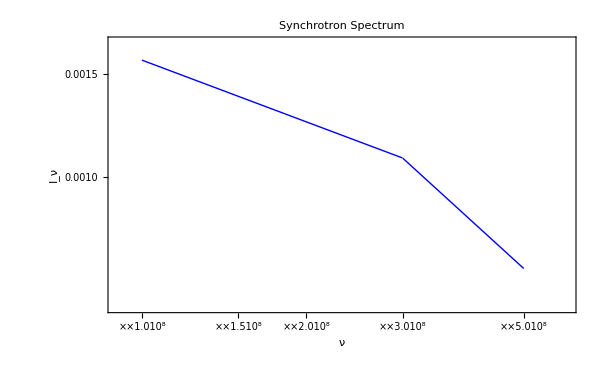

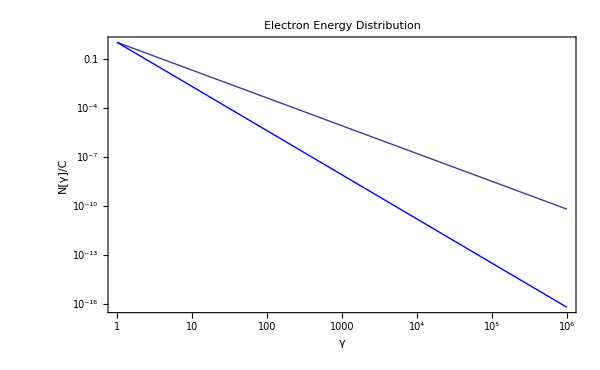

(2.46966×10^13)/(B^2 γ)

```mathematica
Remove["Global`*"]
MHz=10^6;
P[ν_]=Piecewise[{{C1 (ν )^(-.35), ν ≤ 300 MHz}, {C2 (ν )^(-.85), ν≥  300 MHz}}];
P[ν_]=P[ν]/.Solve[C1 (300 MHz)^(-.35)==C2 (300 MHz )^(-.85),C2][[1]]/.C1->1;
LogLogPlot[P[ν],{ν,100 MHz,500 MHz},PlotStyle->{Thick,Blue},PlotRange->{{90 MHz ,600 MHz },{0.0006,.0017}},Frame->True,FrameLabel->{Style["ν",20],Style["I_ν",20]},PlotLabel->Style["Synchrotron Spectrum",25],ImageSize->600]
LogLogPlot[{γ^-1.7,γ^-2.7},{γ,1,10^6},PlotStyle->{Thick,Blue},Frame->True,FrameLabel->{Style["γ",20],Style["N[γ]/C",20]},PlotLabel->Style["Electron Energy Distribution",25],ImageSize->600]
t[γ_]=(2.4696644183994668*^13)/(B^2 γ)
```

98786.6

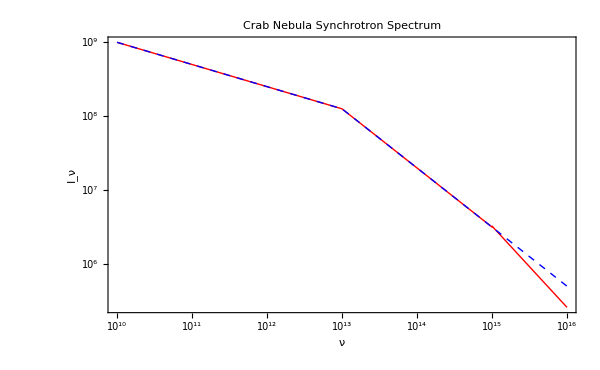

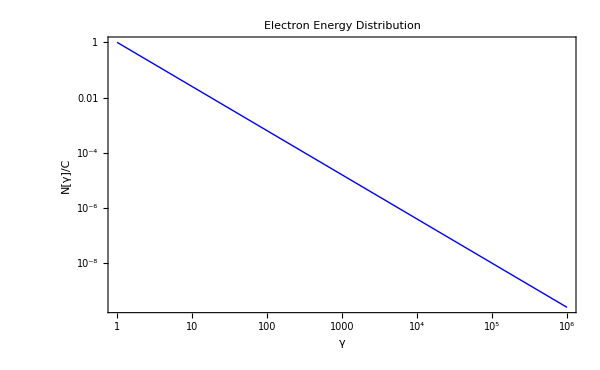

4.13905×10^22

```mathematica
Remove["Global`*"]
b=10^13;
t=1000;
B=500;
γ=(2.4696644183994668*^13)/(B^2 t)

P[ν_]=Piecewise[{{C1 (ν )^(-.3), ν ≤ b}, {C2 (ν )^(-.8), b≤ν≤ 100b}, {C3 ( (ν )^-1.1-(ν b)^-1.2), ν≥ 100 b}}];
P2[ν_]=Piecewise[{{C1 (ν )^(-.3), ν ≤ b}, {C2 (ν )^(-.8), b≤ν≤ 100b}, {C3 (ν)^(-.8), ν≥ 100 b}}];
P[ν_]=P[ν]/.Solve[{C1 (b)^(-.3)==C2 (b)^(-.8),C2 (10^2 b)^(-.8)==C3 ((10^2 b)^-1.1-(10^2 b)^-1.2)},{C2,C3}][[1]]/.C1->10^12;
P2[ν_]=P2[ν]/.Solve[{C1 (b)^(-.3)==C2 (b)^(-.8),C2 (10^2 b)^(-.8)==C3 (10^2 b)^(-.8)},{C2,C3}][[1]]/.C1->10^12;

LogLogPlot[{P[ν],P2[ν]},{ν,.001b,1000b},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},Frame->True,FrameLabel->{Style["ν",20],Style["I_ν",20]},PlotLabel->Style["Crab Nebula Synchrotron Spectrum",25],ImageSize->600,Exclusions->None]
LogLogPlot[ γ^-1.6,{γ,1,10^6},PlotStyle->{Thick,Blue},Frame->True,FrameLabel->{Style["γ",20],Style["N[γ]/C",20]},PlotLabel->Style["Electron Energy Distribution",25],ImageSize->600]
ω=(5.27*10^17)(.5*10^-3)(10^4)^2/2π
```

```mathematica
Remove["Global`*"]
m=9.109*10^-28
q=4.8*10^-10
c=2.998*10^10
γ[t]=((4*10^-12)/9(q^4/(m^3 c^5))B^2 t)^-1
(t/(π*10^7))/.Solve[γ[t]==γ,t]
q/m
```

9.109×10^-28

4.8×10^-10

2.998×10^10

Set::write: Tag Real in 98786.6[1000] is Protected.

3.10347×10^12

Solve::ivar: 1000 is not a valid variable.

ReplaceAll::reps: {Solve[98786.6[1000] == 98786.6, 1000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(10000 π)/.Solve[98786.6[1000]==98786.6,1000]

5.26951×10^17

```mathematica
Remove["Global`*"]
m=9.109*10^-28;
q=4.8*10^-10;
c=2.998*10^10;
z=.835;
νa=10^9.5;
νm=10^11;
νc=10^14;
νa0=νa (1+z);
νm0=νm (1+z);
νc0=νc(1+z);
t=.033;
B=1.5*10^5;
γ[ν_]=((m c)/(q (B*10^-6)))^(1/2)(2π ν)^(1/2);
γ[νm0]
γ[νc0]

t=.033;
B=1.5*10^5;
γ2=(2.4696644183994668*^13)/(B^2 t)
```

661.291

20911.9

33261.5